# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

iaa=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ibb=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
iccolor=reduire[clean@Import[pathResult],reduce];

Show[iaa]
```

-Graphics-

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{500,500}}
ims=Table[
nx=dims[[1]]/reduce;
ny=dims[[2]]/reduce;


{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{iaa,ibb,iccolor};
{ia,ib}
,{dims,listDims}]
```

{{500,500}}

{{-Graphics-,-Graphics-}}

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
bigTest[steps_,dis_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
ic=move[im[[1]],dis];
depth=stereoDepth[n,u,listv0,condition,im[[1]],ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,45}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.1:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
(* Test values *)
testLevels={{1,1}};
dis=0.1;
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
v0List={{0,0.5},{-0.5,0.5},{0,1},{-1,1},{0,2},{-2,2}};
```

```mathematica
(* Creating condition *)
topbot={-2,2};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Scaling results *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
levelTable=Table[Table[

(* Creating initial values *)
range=v0;
r=Random[];
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];

bigTest[steps,dis,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}],{v0,v0List}];
```

```mathematica
(*selectrion criteria, level, image, extra, kind of result, rows *)
Dimensions[levelTable]
```

{6,1,1,1,4}

### Histogram Grid 1

```mathematica
fontsize=20;
imagesize=500;
maxvalue={{-0.1,1.1},{0,800}};
bar=65;
```

```mathematica
histogramGrid=Table[
Table[

convergedData=Flatten[levelTable[[which,idxims,1,1,1,All,All,2]]];
okData=Flatten[levelTable[[which,idxims,1,1,2,All,All,2]]];
nonConvergedData=Flatten[levelTable[[which,idxims,1,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Length[Flatten[DeleteDuplicates[#]&/@Round[levelTable[[which,idxims,1,1,1,All,All,1]]]]])/(103.*45.);
meanError=Mean[Abs[0.1-convergedData]];

Histogram[{convergedData, nonConvergedData,okData},bar,
PlotLabel->Column[{
Style[Row[{"v0 range= ","[",Row[v0List[[which]],","],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Mean error= ",NumberForm[meanError,2]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen}]
,{which,{1,4,5}(*Length[v0List]*)}],{idxims,Length[ims]}];
```

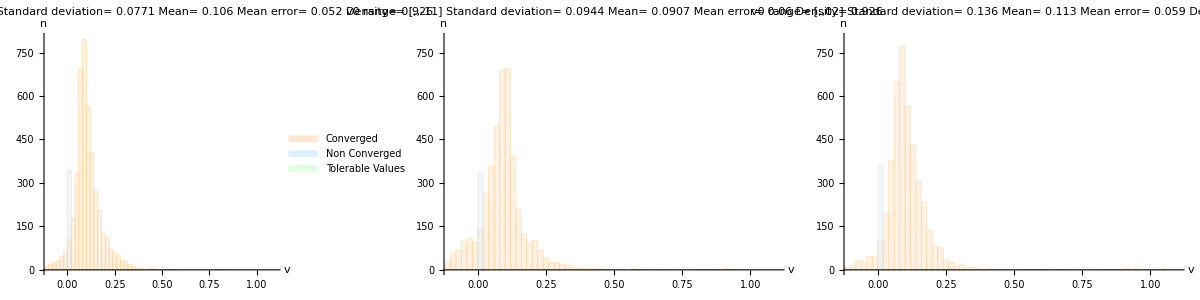

```mathematica
hFinal=Legended[
Grid[histogramGrid],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{"Converged", "Non Converged", "Tolerable Values"},LegendLayout->"Row"],Below]]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-hist.pdf"}],hFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-range-hist.pdf

### Images

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
imagesTable=Table[

{levelTable[[which,1,1,1,4]],Style[Style[Row[{"v0 range= ","[",Row[v0List[[which]],","],"]"}],FontSize->fontsize,FontFamily->"Times",Italic],FontSize->fontsize,FontFamily->"Times",Italic]}

,{which,{1,4,5}(*Length[v0List]*)}];

imFinal=Legended[Grid[Flatten[imagesTable,{{2},{1}}]],legendBar]
```

-Graphics- | -Graphics- | -Graphics-
v0 range= [,,00.5] | v0 range= [,,-11] | v0 range= [,,02]

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-range-im.pdf

### Table

```mathematica
tableValues=Table[
Table[

convergedData=Flatten[levelTable[[which,idxims,1,1,1,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Length[Flatten[DeleteDuplicates[#]&/@Round[levelTable[[which,idxims,1,1,1,All,All,1]]]]])/(103.*45.);
meanError=Mean[Abs[0.1-convergedData]];

{std,mu,density,meanError}

,{idxims,Length[ims]}],{which, Length[v0List]}];
```

```mathematica
makeTable=Table[
values=tableValues[[All,All,which]];
If[which==3,
greenRedColor[z_]:=Blend[{Red,Green},Rescale[z,MinMax[values],{0,1}]];
,
If[which==2,
greenRedColor[z_]:=Blend[{Green,Red},Rescale[z,MinMax[Abs[dis-Abs[values]]],{0,1}]];
,
greenRedColor[z_]:=Blend[{Green,Red},Rescale[z,MinMax[values],{0,1}]];
];
];


TableForm@Map[Item[#,
Background->Directive[Opacity[0.7],
greenRedColor[#]]
]&,
If[which==2,Abs[dis-Abs[values]],values],
{2}]

,{which, Dimensions[tableValues][[3]]}];

t=Prepend[{makeTable},{"std","dis-mu","density","muerror"}];
t2=MapThread[Prepend,{t,{"v0 Range",Table[{Row[v0List[[i]],","]},{i,Length[v0List]}]//TableForm}}];
tFinal=Grid[t2]
```

v0 Range | std | dis-mu | density | muerror
,,00.5
,,-0.50.5
,,01
,,-11
,,02
,,-22 | 0.0771035
0.0797238
0.0893175
0.0944323
0.136468
0.137632 | 0.00612076
0.012752
0.00829608
0.00932245
0.0130163
0.00464551 | 0.925782
0.927724
0.924919
0.925998
0.916505
0.926429 | 0.0521351
0.0537718
0.054341
0.0601612
0.058576
0.0664717

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-tbl.pdf"}],tFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-range-tbl.pdf

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=45;
{ka,kb}=ImageData[#][[k]]&/@{ia,move[ia,dis]};
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && -2<Total[x[[1;;2]]]<2;
```

```mathematica
range={-2,2};
r=Random[];
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
```

```mathematica
lineTest[n,u,listv0,condition,Range[1,ImageDimensions[ia][[1]]],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```

{{0.0859147,0.0521268,converged,1},{0.0146518,0.0178445,converged,2},{0.0404445,0.0416144,converged,3},{0.0525009,0.0540278,converged,4},{0.055104,0.0536714,converged,5},{0.0454186,0.045773,converged,6},{0.0492589,0.0499865,converged,7},{0.131675,0.00865422,ok,8},{0.0252302,0.0242721,converged,9},{0.106288,0.100689,converged,10},{0.00590948,0.00982105,converged,11},{0.0419427,0.0434914,converged,12},{0.059317,0.0630068,converged,13},{-0.0623406,-0.073265,ok,14},{0.0285932,0.0302216,converged,15},{0.0514342,0.0556894,converged,16},{0.137891,0.0171454,ok,17},{0.0274563,0.0274246,converged,18},{0.0540107,0.0582663,converged,19},{0.0892412,0.0864537,converged,20},{0.,0.,sign,21},{0.00947829,0.0141833,converged,22},{0.0442934,0.0498272,converged,23},{0.0822999,0.0881292,converged,24},{-0.00536281,-0.0183951,converged,25},{0.040969,0.0417692,converged,26},{0.0583445,0.067992,converged,27},{-0.01462,-0.0253441,converged,28},{0.0559549,0.0824179,converged,29},{-0.048873,-0.0176295,converged,30},{0.0307825,0.0301797,converged,31},{0.0582774,0.0643014,converged,32},{0.0259277,0.0330409,converged,33},{0.0374295,0.0380094,converged,34},{0.0572206,0.0621375,converged,35},{0.150292,0.11193,converged,36},{0.00638633,0.0099481,converged,37},{0.0437674,0.0458663,converged,38},{0.0466445,0.0471367,converged,39},{0.0345005,0.0372105,converged,40},{0.0426475,0.0426623,converged,41},{0.0545682,0.0566682,converged,42},{0.160187,0.163132,converged,43},{0.0230574,0.0235685,converged,44},{0.0562285,0.0612154,converged,45},{0.0781085,0.070223,converged,46},{0.0157439,0.0220015,converged,47},{0.0356977,0.0373339,converged,48},{0.0498708,0.0510458,converged,49},{0.0605074,0.0614889,converged,50},{0.0695351,0.0647551,converged,51},{0.0787443,0.0808826,converged,52},{0.0853741,0.0651955,converged,53},{0.0291137,0.0301006,converged,54},{0.0579842,0.0674209,converged,55},{0.0391352,0.0433546,converged,56},{0.0449344,0.0530684,converged,57},{0.,0.,sign,58},{0.0295549,0.028143,converged,59},{0.05801,0.0683912,converged,60},{0.240546,0.0934882,converged,61},{0.00420819,0.0142907,converged,62},{0.0218824,0.0270281,converged,63},{0.035076,0.0349984,converged,64},{0.0576283,0.0664973,converged,65},{-0.0400907,-0.0784592,converged,66},{0.0435528,0.0533238,converged,67},{0.0828563,0.0748189,converged,68},{0.161005,0.00956609,ok,69},{0.0352819,0.0476002,converged,70},{0.0567928,0.0536682,converged,71},{0.106508,0.0454619,ok,72},{0.0301173,0.0333306,converged,73},{0.0193502,0.025024,converged,74},{0.0422718,0.0438205,converged,75},{0.0694583,0.0837473,converged,76},{0.00439764,0.00246194,converged,77},{0.0377597,0.0378941,converged,78},{0.0631464,0.0737333,converged,79},{0.700518,1.03383,converged,80},{-0.021566,-0.0235073,converged,81},{0.0456483,0.0553138,converged,82},{0.166252,0.112161,converged,83},{0.00308352,0.0105272,converged,84},{0.0338313,0.0353592,converged,85},{0.0502558,0.0529999,converged,86},{0.0715107,0.0726725,converged,87},{0.193154,0.198457,converged,88},{0.0164634,0.0189384,converged,89},{0.0473863,0.0496404,converged,90},{0.0236935,0.027409,converged,91},{0.0482967,0.0549168,converged,92},{0.154378,0.137792,converged,93},{-0.0384883,-0.010565,converged,94},{0.022089,0.0243562,converged,95},{0.0498449,0.0563217,converged,96},{0.085309,0.0812109,converged,97},{-0.0341318,-0.0567733,converged,98},{0.0330659,0.03532,converged,99},{0.0414318,0.0426508,converged,100},{0.046949,0.0476172,converged,101},{0.0617179,0.0671737,converged,102},{-0.0243109,-0.0221255,converged,103}}

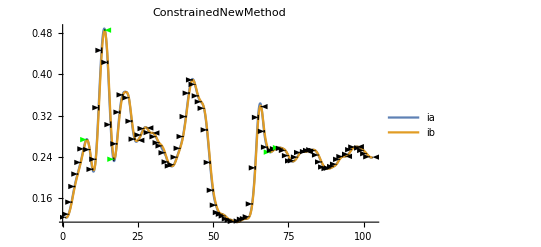

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```